# Mass Running

## Initialization

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/tom/Uni/phd/PhD_thesis/thesis/programs/c++/decoupling

```mathematica
<</home/tom/Documents/software/software/RunDec.m
```

RunDec: a Mathematica package for running and decoupling of the

strong coupling and quark masses

by K.G. Chetyrkin, J.H. K\"uhn and M. Steinhauser (January 2000)

by F. Herren and M. Steinhauser (April 2016, v2.1)

```mathematica
alphas=0.118002; 
MZ = 91.1876;
mt = 162.7;
mb = 4.18;
```

```mathematica
asmt = AlphasExact[alphas, MZ, mt, 5, 4]
```

0.108523

```mathematica
asmb = AlphasExact[alphas, MZ, mb, 5, 4]
```

0.224624

## Top-quark mass

```mathematica
mts ={};
mbs = {}; 
alphass = {};
mus = {};
Do[mtNew = AsmMSrunexact[mt, asmt, mt, muR, 5, 4];
AppendTo[mts, mtNew[[1]]];
AppendTo[alphass, mtNew[[2]]]; 
mbNew = AsmMSrunexact[mb, asmb, mb, muR, 5, 4];
AppendTo[mbs, mbNew[[1]]];
AppendTo[mus, muR] , {muR,5, 1000}]
```

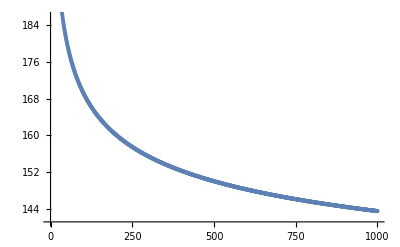

```mathematica
ListPlot[Transpose[{mus, mts}]]
```

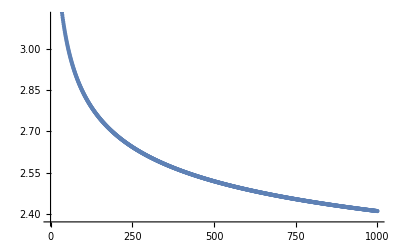

```mathematica
ListPlot[Transpose[{mus, mbs}]]
```

```mathematica
Export["../../../figures/running/running4l_RunDec.csv",Transpose[{mus,mbs,mts, alphass}]]
```

../../../figures/running/running4l_RunDec.csv